### Base case: constant growth c1 & constant sloughing c2<c1

#### Setup

```mathematica
ClearAll["Global`*"];Remove["Global`*"];

RodOde[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=Block[{x,y,θ,m,S},
sol=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x,y,θ,m},{S,0,LR}][[1]];
{x[S]-L0,y[S],θ[S]}/.sol/.S->LR];

RodShape[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x[S],y[S],θ[S],m[S]},{S,0,LR}][[1]];
```

#### Evolving shape

Parameters

```mathematica
L0=1;
Subscript[c, 1]=1.2; (* growth rate *)
Subscript[c, 2]=1; (* sloughing rate *)
dt=0.1;
```

First step

```mathematica
i=1;
t=i dt;
γ=1+Subscript[c, 1] t;
LR=L0-(Subscript[c, 2] t)/(1+Subscript[c, 1] t);
```

```mathematica
Subscript[S, 1]=FindRoot[RodOde[a,b,c,LR],{a,-5},{b,-2},{c,0.1}]
```

{a→-9.5804,b→-0.865767,c→0.180737}

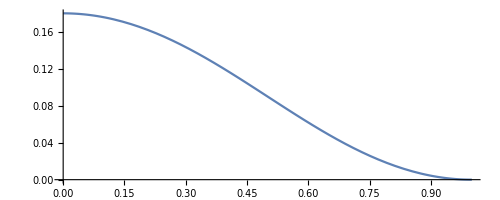

```mathematica
Subscript[Sol, 1]=RodShape[a/. Subscript[S, 1],b/. Subscript[S, 1],c/. Subscript[S, 1],LR];
ParametricPlot[Evaluate[{x[S],y[S]}/. Subscript[Sol, 1]],{S,0,LR}]
```

Now iterate

```mathematica
NN=10;
For[i=2,i≤NN,i++,
t=i dt;
γ=1+Subscript[c, 1] t;
LR=L0-(Subscript[c, 2] t)/(1+Subscript[c, 1] t);
Subscript[S, i]=FindRoot[RodOde[a,b,c,LR],{a,a/. Subscript[S, i-1]},{b,b/. Subscript[S, i-1]},{c,c/. Subscript[S, i-1]}];
]
```

```mathematica
Manipulate[t=i dt;
γ=1+Subscript[c, 1] t;
LR=L0-(Subscript[c, 2] t)/(1+Subscript[c, 1] t);
Sol=RodShape[a/. Subscript[S, i],b/. Subscript[S, i],c/. Subscript[S, i],LR];
ParametricPlot[Evaluate[{x[S],y[S]}/.Sol],{S,0,LR}],{i,1,NN,1}]
```

### Eventual steady state: constant growth c1 & ramped sloughing up to c1

#### Setup

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"];Remove["Global`*"];

RodOde[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=Block[{x,y,θ,m,S},
sol=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x,y,θ,m},{S,0,LR}][[1]];
{x[S]-L0,y[S],θ[S]}/.sol/.S->LR];

RodShape[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x[S],y[S],θ[S],m[S]},{S,0,LR}][[1]];
```

#### Evolving shape

Parameters

```mathematica
L0=1;
Subscript[c, 1]=1.0; (* growth rate *)
σ=10; (* sloughing rate *)
T=1.0;
dt=0.05;
```

Sloughing rate function

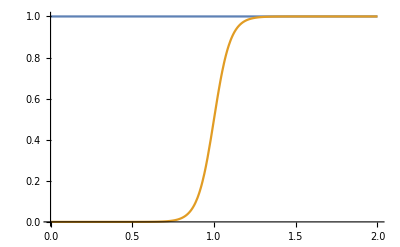

```mathematica
μ[σ_,t_,T_]:=Subscript[c, 1] 1/2(1.0+Tanh[σ(t-T)]);
Plot[{Subscript[c, 1],μ[σ,t,T]},{t,0,2.0}]
```

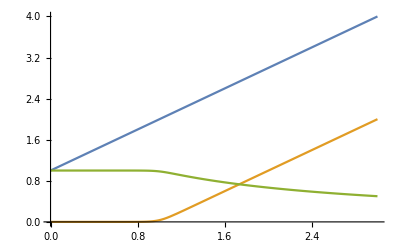

```mathematica
lr[t_]:=NIntegrate[μ[σ,s,T],{s,0,t}];
g[t_]:=1+Subscript[c, 1] t;
Lr[t_]:=L0-lr[t]/g[t];
Plot[{g[t],lr[t], Lr[t]},{t,0,3.0}]
```

```mathematica
i=1;
t=i dt;
γ=g[t]
LR=L0-lr[t]/g[t]
```

1.05

1.

{a→-9.17104,b→-1.3177,c→0.287362}

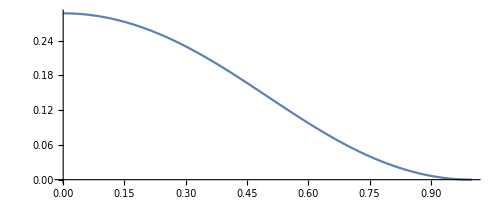

```mathematica
Subscript[S, 1]=FindRoot[RodOde[a,b,c,LR],{a,-5},{b,-2},{c,0.1}]
Subscript[Sol, 1]=RodShape[a/. Subscript[S, 1],b/. Subscript[S, 1],c/. Subscript[S, 1],LR];
ParametricPlot[Evaluate[{x[S],y[S]}/. Subscript[Sol, 1]],{S,0,LR}]
```

Now iterate

```mathematica
NN=100;
For[i=2,i≤NN,i++,
t=i dt;
γ=g[t];
LR=L0-lr[t]/g[t];
Subscript[S, i]=FindRoot[RodOde[a,b,c,LR],{a,a/. Subscript[S, i-1]},{b,b/. Subscript[S, i-1]},{c,c/. Subscript[S, i-1]}];
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Manipulate[t=i dt;
γ=g[t];
LR=L0-lr[t]/g[t];
Sol=RodShape[a/. Subscript[S, i],b/. Subscript[S, i],c/. Subscript[S, i],LR];
Show[ParametricPlot[Evaluate[{x[S],y[S]}/.Sol],{S,0,LR},PlotRange->{0,2.0}],
Graphics[{Blue,Disk[Evaluate[{x[S],y[S]}/.Sol/.S->0.1],0.04]}],
Graphics[{Red,Disk[Evaluate[{x[S],y[S]}/.Sol/.S->0.3],0.04]}],
Graphics[{Green,Disk[Evaluate[{x[S],y[S]}/.Sol/.S->0.5],0.04]}]
],{i,1,NN,1}]
```

```mathematica
AgeSols = DSolve[{A'[t]==1-γ'[t]/γ[t]*A[t],γ'[t]==g,A[0]==0, γ[0]==1},{A[t], γ[t]}, t][[1]]
```

{γ[t]→1+g t,A[t]→(2 t+g t^2)/(2 (1+g t))}

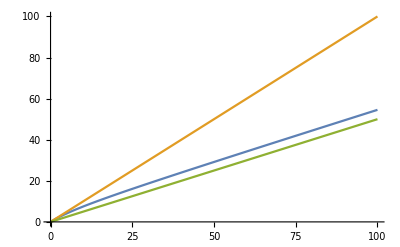

```mathematica
Plot[{A[t]/.AgeSols/.g-> 0.1, t, t/2},{t,0,100}]
```